```mathematica
Integrate[q q/(en-q q),q]
```

-q+√en ArcTanh[q/(√en)]

```mathematica
f=(x^(1/2))/(2x+1)^2;f2=(x^(1/2))/(2x+1)^3
```

(√x)/(1+2 x)^3

```mathematica
Integrate[f2,x]
```

(2 √x (-1+2 x)+√2 (1+2 x)^2 ArcTan[√2 √x])/(16 (1+2 x)^2)

```mathematica
Integrate[f,{x,0,1}]
```

If[Re[a]≥2||Re[a]≤0||a∉Reals,1/4 (2/(-2+a)-(√2 ArcTanh[(√2)/(√a)])/(√a)),Integrate[(√x)/(a-2 x)^2,{x,0,1},Assumptions→!(Re[a]≥2||Re[a]≤0||a∉Reals)]]

```mathematica
FullSimplify[%%,a<0]
```

1/4 (2/(-2+a)-(√2 ArcTanh[(√2)/(√a)])/(√a))

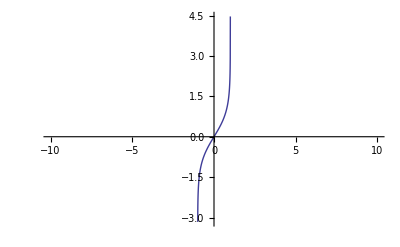

```mathematica
Plot[ArcTanh[x],{x,-10,10}]
```

```mathematica
ArcTanh[1000.]
```

0.001-1.5708 ⅈ

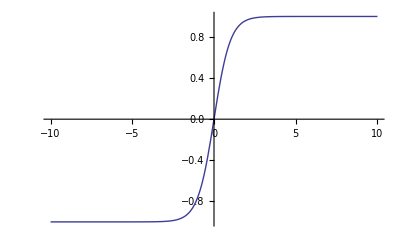

```mathematica
Plot[Tanh[x],{x,-10,10}]
```

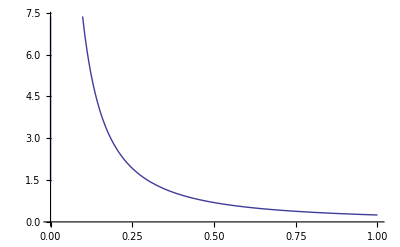

```mathematica
Plot[f/.{a->-0.01},{x,0,1}]
```

```mathematica
g[n_]:=NIntegrate[y^(1/2)/(y+1)^(1+n),{y,0,0.1}]
```

```mathematica
g[1]
```

0.0187976

```mathematica
g[2]
```

0.0177667

```mathematica
g[3]
```

0.0168029

```mathematica
fs=y^(1/2)/(y+1)^(1+n)
```

√y (1+y)^(-1-n)

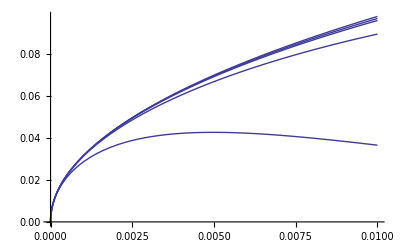

```mathematica
Plot[fs/.n->{1,2,3,10,100},{y,0,0.01}]
```

```mathematica
NIntegrate[(√y)/(1+y)^3,{y,0,0.1}]
```

0.0177667

```mathematica
fs/.n->2
```

(√y)/(1+y)^3

```mathematica
f1=(ekq-ek)(dk ekq+dkq ek)-(ek Ekq+ekq Ek)(dkq-dk)
```

(-ek+ekq) (dkq ek+dk ekq)-(-dk+dkq) (Ek ekq+ek Ekq)

```mathematica
f2=(ekq+ek)(dk ekq-dkq ek)+(ek Ekq-ekq Ek)(dkq+dk)
```

(ek+ekq) (-dkq ek+dk ekq)+(dk+dkq) (-Ek ekq+ek Ekq)

```mathematica
f1-f2
```

-(ek+ekq) (-dkq ek+dk ekq)+(-ek+ekq) (dkq ek+dk ekq)-(dk+dkq) (-Ek ekq+ek Ekq)-(-dk+dkq) (Ek ekq+ek Ekq)

```mathematica
Simplify[%]
```

2 (dk (-ek+Ek) ekq+dkq ek (ekq-Ekq))

```mathematica
FullSimplify[%]
```

2 (dk (-ek+Ek) ekq+dkq ek (ekq-Ekq))

```mathematica
%/.{Ekq->(ekq^2+dkq^2)^(1/2),Ek->(ek^2+dk^2)^(1/2)}
```

2 (dk (-ek+√(dk^2+ek^2)) ekq+dkq ek (ekq-√(dkq^2+ekq^2)))

```mathematica
Simplify[%%]
```

2 (dk (-ek+√(dk^2+ek^2)) ekq+dkq ek (ekq-√(dkq^2+ekq^2)))

```mathematica
Integrate[k^2/(k^2+K^2)^2,{k,0,Infinity}]
```

If[Re[K]>0,π/(4 K),Integrate[k^2/((k^2+K^2)^2),{k,0,∞},Assumptions→Re[K]≤0]]

```mathematica
T={{ek-ekq,0,-Ikq,Ik},{0,-ek+ekq,-Ik,Ikq},{-Ikq,-Ik,-ekq-ek,0},{Ik,Ikq,0,ekq+ek}}
```

{{ek-ekq,0,-Ikq,Ik},{0,-ek+ekq,-Ik,Ikq},{-Ikq,-Ik,-ek-ekq,0},{Ik,Ikq,0,ek+ekq}}

```mathematica
FullSimplify[Eigensystem[T]]
```

{{-√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2))),√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2))),-√(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2))),√(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))},{{(ek^2 ekq-√((ekq^2+Ik^2) (ek^2+Ikq^2)) √(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))+ekq (Ikq^2-√((ekq^2+Ik^2) (ek^2+Ikq^2)))+ek (-Ik^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))-ekq (ekq+√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))))/(Ik (-Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))+ek (-ek+√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))))),(Ikq √(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))/(-Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))+ek (-ek+√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))),(Ikq (Ik^2-√((ekq^2+Ik^2) (ek^2+Ikq^2))+ekq (ekq+√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))))/(Ik (-Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))+ek (-ek+√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))))),1},{(ek^2 ekq+√((ekq^2+Ik^2) (ek^2+Ikq^2)) √(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))+ekq (Ikq^2-√((ekq^2+Ik^2) (ek^2+Ikq^2)))+ek (-Ik^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))+ekq (-ekq+√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))))/(Ik (-Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))-ek (ek+√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))))),(Ikq √(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))/(Ikq^2-√((ekq^2+Ik^2) (ek^2+Ikq^2))+ek (ek+√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))),(Ikq (ekq^2+Ik^2-√((ekq^2+Ik^2) (ek^2+Ikq^2))-ekq √(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))))/(Ik (-Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))-ek (ek+√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))))),1},{-(ek^2 ekq+ekq (Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2)))+√((ekq^2+Ik^2) (ek^2+Ikq^2)) √(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))-ek (Ik^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))+ekq (ekq+√(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))))/(Ik (ek^2+Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))-ek √(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))),-(Ikq √(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))/(ek^2+Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))-ek √(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))),-(Ikq (Ik^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))+ekq (ekq+√(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))))/(Ik (ek^2+Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))-ek √(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))),1},{(-ek^2 ekq-ekq (Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2)))+√((ekq^2+Ik^2) (ek^2+Ikq^2)) √(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))+ek (ekq^2+Ik^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))-ekq √(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))))/(Ik (Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))+ek (ek+√(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))))),(Ikq √(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))/(Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))+ek (ek+√(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2))))),-(Ikq (ekq^2+Ik^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))-ekq √(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))))/(Ik (Ikq^2+√((ekq^2+Ik^2) (ek^2+Ikq^2))+ek (ek+√(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))))),1}}}

```mathematica
Solve[detT==0,v]
```

{{v→-√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))},{v→√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))},{v→-√(ek^2+ekq^2+Ik^2+Ikq^2+2 √(ek^2 ekq^2+ek^2 Ik^2+ekq^2 Ikq^2+Ik^2 Ikq^2))},{v→√(ek^2+ekq^2+Ik^2+Ikq^2+2 √(ek^2 ekq^2+ek^2 Ik^2+ekq^2 Ikq^2+Ik^2 Ikq^2))}}

```mathematica
FullSimplify[%]
```

{{v→-√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))},{v→√(ek^2+ekq^2+Ik^2+Ikq^2-2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))},{v→-√(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))},{v→√(ek^2+ekq^2+Ik^2+Ikq^2+2 √((ekq^2+Ik^2) (ek^2+Ikq^2)))}}

```mathematica
T3={{eapq-eap,0,0,dfpq,-dfp,dgpq,-dgp},{0,ebp-ebpq,0,dfp,-dfpq,0,0},
{0,0,ecp-ecpq,0,0,dgp,-dgpg},
{dfpq,dfp,0,-eap-ebpq,0,0,0},
{-dfp,-dfpq,0,0,eapq+eap,0,0},
{dgpq,0,dgp,0,0,-eap-ecpq,0},
{-dgp,0,-dgpq,0,0,0,eapq+ecp}};MatrixForm[T31-IdentityMatrix[7]*v]
```

(-eap+eapq | 0 | 0 | dfpq | -dfp | dgpq | -dgp
0 | ebp-ebpq | 0 | dfp | -dfpq | 0 | 0
0 | 0 | ecp-ecpq | 0 | 0 | dgp | -dgpg
dfpq | dfp | 0 | -eap-ebpq | 0 | 0 | 0
-dfp | -dfpq | 0 | 0 | eap+eapq | 0 | 0
dgpq | 0 | dgp | 0 | 0 | -eap-ecpq | 0
-dgp | 0 | -dgpq | 0 | 0 | 0 | eapq+ecp)

```mathematica
T31=T3/.{ecpq->eapq,ecp->ecp,ebpq->eapq,ebp->ebq}
```

{{-eap+eapq,0,0,dfpq,-dfp,dgpq,-dgp},{0,-eapq+ebq,0,dfp,-dfpq,0,0},{0,0,-eapq+ecp,0,0,dgp,-dgpg},{dfpq,dfp,0,-eap-eapq,0,0,0},{-dfp,-dfpq,0,0,eap+eapq,0,0},{dgpq,0,dgp,0,0,-eap-eapq,0},{-dgp,0,-dgpq,0,0,0,eapq+ecp}}

```mathematica
Eigenvalues[T31]
```

{Root[dfp^2 dgp^4 eap-dfpq^2 dgp^4 eap-dfp^4 dgpg dgpq eap+«261»+(2 eap+eapq-ebq-2 ecp) #1^6+#1^7&,1],Root[«1»&,2],«4»,Root[«267»+(«2»)^7&,7]}

```mathematica
dt3=Det[T311-IdentityMatrix[7]*v]
```

-dgp (dgp (dfp (dfp dgp^2-dfp dgp dgpq) (-eap-eapq-v)+(-dfp (-dfp dgp^2+dfp dgp dgpq)-(dgp^2-dgp dgpq) (-eap-eapq-v) (-eapq+ebq-v)) (eap+eapq-v))+(-eap-eapq-v) (-eapq+ecp-v) (dgp eap^2 eapq+2 dgp eap eapq^2+dgp eapq^3-dgp eap^2 ebq-2 dgp eap eapq ebq-dgp eapq^2 ebq+2 dfp^2 dgp v+dgp eap^2 v+2 dgp eap eapq v+dgp eapq^2 v-dgp eapq v^2+dgp ebq v^2-dgp v^3))-dgpq (-dgpq (dfp (dfp dgp^2-dfp dgp dgpq) (-eap-eapq-v)+(-dfp (-dfp dgp^2+dfp dgp dgpq)-(dgp^2-dgp dgpq) (-eap-eapq-v) (-eapq+ebq-v)) (eap+eapq-v))+dgp (-eap-eapq-v) (-dfp (-eap-eapq-v) (-dfp eapq+dfp ebq-dfp v)-dfp (dfp eap^2-dfp eapq^2+2 dfp eap v+dfp v^2)+(eap+eapq-v) (-dfp (-dfp eap+dfp eapq-dfp v)+(-eapq+ebq-v) (-dfp^2+eap^2-eapq^2+2 eap v+v^2))))+(eapq+ecp-v) (-dgp^2 (-dfp (-eap-eapq-v) (-dfp eapq+dfp ebq-dfp v)-dfp (dfp eap^2-dfp eapq^2+2 dfp eap v+dfp v^2)+(eap+eapq-v) (-dfp (-dfp eap+dfp eapq-dfp v)+(-eapq+ebq-v) (-dfp^2+eap^2-eapq^2+2 eap v+v^2)))+(-eapq+ecp-v) (dgpq (-dgpq eap^2 eapq-2 dgpq eap eapq^2-dgpq eapq^3+dgpq eap^2 ebq+2 dgpq eap eapq ebq+dgpq eapq^2 ebq-2 dfp^2 dgpq v-dgpq eap^2 v-2 dgpq eap eapq v-dgpq eapq^2 v+dgpq eapq v^2-dgpq ebq v^2+dgpq v^3)+(-eap-eapq-v) (-dfp (-eap-eapq-v) (-dfp eapq+dfp ebq-dfp v)-dfp (dfp eap^2-dfp eapq^2+2 dfp eap v+dfp v^2)+(eap+eapq-v) (-dfp (-dfp eap+dfp eapq-dfp v)+(-eapq+ebq-v) (-dfp^2+eap^2-eapq^2+2 eap v+v^2)))))

```mathematica
FullSimplify[dt3]
```

dgp^2 (2 dfp^2 v+(eap+eapq-v) (eap+eapq+v) (eapq-ebq+v)) (dgp^2-dgp dgpq-(eap+eapq+v) (eapq-ecp+v))-dgpq (dgp (-eap-eapq-v) (-(eap-eapq) (eap+eapq)^2 (eapq-ebq)-(2 dfp^2+(eap+eapq)^2) (eap-ebq) v-(4 dfp^2+eap^2+eapq (2 eapq-ebq)+eap (eapq+ebq)) v^2+(eap-ebq) v^3+v^4)+dgp (dgp-dgpq) dgpq (2 dfp^2 v+(eap+eapq-v) (eap+eapq+v) (eapq-ebq+v)))+(eapq+ecp-v) (-dgp^2 (-(eap-eapq) (eap+eapq)^2 (eapq-ebq)-(2 dfp^2+(eap+eapq)^2) (eap-ebq) v-(4 dfp^2+eap^2+eapq (2 eapq-ebq)+eap (eapq+ebq)) v^2+(eap-ebq) v^3+v^4)+(-eapq+ecp-v) ((-eap-eapq-v) (-(eap-eapq) (eap+eapq)^2 (eapq-ebq)-(2 dfp^2+(eap+eapq)^2) (eap-ebq) v-(4 dfp^2+eap^2+eapq (2 eapq-ebq)+eap (eapq+ebq)) v^2+(eap-ebq) v^3+v^4)+dgpq^2 (-2 dfp^2 v-(eap+eapq-v) (eap+eapq+v) (eapq-ebq+v))))

```mathematica
MatrixForm[T31-IdentityMatrix[7]*v]
```

(-eap+eapq-v | 0 | 0 | dfpq | -dfp | dgpq | -dgp
0 | -eapq+ebq-v | 0 | dfp | -dfpq | 0 | 0
0 | 0 | -eapq+ecp-v | 0 | 0 | dgp | -dgpg
dfpq | dfp | 0 | -eap-eapq-v | 0 | 0 | 0
-dfp | -dfpq | 0 | 0 | eap+eapq-v | 0 | 0
dgpq | 0 | dgp | 0 | 0 | -eap-eapq-v | 0
-dgp | 0 | -dgpq | 0 | 0 | 0 | eapq+ecp-v)

```mathematica
T311=T31/.{dfpq->dfp,dgpg->dgp}
```

{{-eap+eapq,0,0,dfp,-dfp,dgpq,-dgp},{0,-eapq+ebq,0,dfp,-dfp,0,0},{0,0,-eapq+ecp,0,0,dgp,-dgp},{dfp,dfp,0,-eap-eapq,0,0,0},{-dfp,-dfp,0,0,eap+eapq,0,0},{dgpq,0,dgp,0,0,-eap-eapq,0},{-dgp,0,-dgpq,0,0,0,eapq+ecp}}

```mathematica
Solve[dt3==0,v]
```

{{v→Root[-dgp^4 eap^2 eapq+dgp^3 dgpq eap^2 eapq+dgp^2 dgpq^2 eap^2 eapq-dgp dgpq^3 eap^2 eapq+dgp dgpq eap^4 eapq-2 dgp^4 eap eapq^2+2 dgp^3 dgpq eap eapq^2+2 dgp^2 dgpq^2 eap eapq^2-2 dgp dgpq^3 eap eapq^2+2 dgp dgpq eap^3 eapq^2-dgp^4 eapq^3+dgp^3 dgpq eapq^3+dgp^2 dgpq^2 eapq^3-dgp dgpq^3 eapq^3+2 dgp^2 eap^2 eapq^3-dgpq^2 eap^2 eapq^3+eap^4 eapq^3+4 dgp^2 eap eapq^4-2 dgp dgpq eap eapq^4-2 dgpq^2 eap eapq^4+2 eap^3 eapq^4+2 dgp^2 eapq^5-dgp dgpq eapq^5-dgpq^2 eapq^5-2 eap eapq^6-eapq^7+dgp^4 eap^2 ebq-dgp^3 dgpq eap^2 ebq-dgp^2 dgpq^2 eap^2 ebq+dgp dgpq^3 eap^2 ebq-dgp dgpq eap^4 ebq+2 dgp^4 eap eapq ebq-2 dgp^3 dgpq eap eapq ebq-2 dgp^2 dgpq^2 eap eapq ebq+2 dgp dgpq^3 eap eapq ebq-2 dgp dgpq eap^3 eapq ebq+dgp^4 eapq^2 ebq-dgp^3 dgpq eapq^2 ebq-dgp^2 dgpq^2 eapq^2 ebq+dgp dgpq^3 eapq^2 ebq-2 dgp^2 eap^2 eapq^2 ebq+dgpq^2 eap^2 eapq^2 ebq-eap^4 eapq^2 ebq-4 dgp^2 eap eapq^3 ebq+2 dgp dgpq eap eapq^3 ebq+2 dgpq^2 eap eapq^3 ebq-2 eap^3 eapq^3 ebq-2 dgp^2 eapq^4 ebq+dgp dgpq eapq^4 ebq+dgpq^2 eapq^4 ebq+2 eap eapq^5 ebq+eapq^6 ebq-2 dgp^2 eap^3 eapq ecp-4 dgp^2 eap^2 eapq^2 ecp-2 dgp^2 eap eapq^3 ecp+2 dgp^2 eap^3 ebq ecp+4 dgp^2 eap^2 eapq ebq ecp+2 dgp^2 eap eapq^2 ebq ecp+dgpq^2 eap^2 eapq ecp^2-eap^4 eapq ecp^2+2 dgpq^2 eap eapq^2 ecp^2-2 eap^3 eapq^2 ecp^2+dgpq^2 eapq^3 ecp^2+2 eap eapq^4 ecp^2+eapq^5 ecp^2-dgpq^2 eap^2 ebq ecp^2+eap^4 ebq ecp^2-2 dgpq^2 eap eapq ebq ecp^2+2 eap^3 eapq ebq ecp^2-dgpq^2 eapq^2 ebq ecp^2-2 eap eapq^3 ebq ecp^2-eapq^4 ebq ecp^2+(-2 dfp^2 dgp^4+2 dfp^2 dgp^3 dgpq+2 dfp^2 dgp^2 dgpq^2-2 dfp^2 dgp dgpq^3-dgp^4 eap^2+2 dfp^2 dgp dgpq eap^2+dgp^3 dgpq eap^2+dgp^2 dgpq^2 eap^2-dgp dgpq^3 eap^2+dgp dgpq eap^4-2 dgp^4 eap eapq+2 dfp^2 dgp dgpq eap eapq+2 dgp^3 dgpq eap eapq+2 dgp^2 dgpq^2 eap eapq-2 dgp dgpq^3 eap eapq+2 dgp^2 eap^3 eapq+4 dgp dgpq eap^3 eapq+2 dfp^2 dgp^2 eapq^2-dgp^4 eapq^2+dgp^3 dgpq eapq^2-2 dfp^2 dgpq^2 eapq^2+dgp^2 dgpq^2 eapq^2-dgp dgpq^3 eapq^2+2 dfp^2 eap^2 eapq^2+6 dgp^2 eap^2 eapq^2+4 dgp dgpq eap^2 eapq^2-dgpq^2 eap^2 eapq^2+eap^4 eapq^2+2 dfp^2 eap eapq^3+6 dgp^2 eap eapq^3-2 dgpq^2 eap eapq^3+4 eap^3 eapq^3+2 dgp^2 eapq^4-dgp dgpq eapq^4-dgpq^2 eapq^4+4 eap^2 eapq^4-eapq^6-2 dfp^2 dgp dgpq eap ebq-2 dgp^2 eap^3 ebq-2 dgp dgpq eap^3 ebq+2 dfp^2 dgp^2 eapq ebq-2 dfp^2 dgp dgpq eapq ebq-4 dgp^2 eap^2 eapq ebq-4 dgp dgpq eap^2 eapq ebq-2 dfp^2 eap eapq^2 ebq-2 dgp^2 eap eapq^2 ebq-2 dgp dgpq eap eapq^2 ebq-2 eap^3 eapq^2 ebq-2 dfp^2 eapq^3 ebq-4 eap^2 eapq^3 ebq-2 eap eapq^4 ebq-4 dfp^2 dgp^2 eap ecp-2 dgp^2 eap^3 ecp-2 dfp^2 dgp^2 eapq ecp-6 dgp^2 eap^2 eapq ecp-2 dgpq^2 eap^2 eapq ecp+2 eap^4 eapq ecp-6 dgp^2 eap eapq^2 ecp-4 dgpq^2 eap eapq^2 ecp+4 eap^3 eapq^2 ecp-2 dgp^2 eapq^3 ecp-2 dgpq^2 eapq^3 ecp-4 eap eapq^4 ecp-2 eapq^5 ecp+2 dfp^2 dgp^2 ebq ecp+2 dgp^2 eap^2 ebq ecp+2 dgpq^2 eap^2 ebq ecp-2 eap^4 ebq ecp+4 dgp^2 eap eapq ebq ecp+4 dgpq^2 eap eapq ebq ecp-4 eap^3 eapq ebq ecp+2 dgp^2 eapq^2 ebq ecp+2 dgpq^2 eapq^2 ebq ecp+4 eap eapq^3 ebq ecp+2 eapq^4 ebq ecp+2 dfp^2 dgpq^2 ecp^2-2 dfp^2 eap^2 ecp^2+dgpq^2 eap^2 ecp^2-eap^4 ecp^2-2 dfp^2 eap eapq ecp^2+2 dgpq^2 eap eapq ecp^2-4 eap^3 eapq ecp^2+dgpq^2 eapq^2 ecp^2-4 eap^2 eapq^2 ecp^2+eapq^4 ecp^2+2 dfp^2 eap ebq ecp^2+2 eap^3 ebq ecp^2+2 dfp^2 eapq ebq ecp^2+4 eap^2 eapq ebq ecp^2+2 eap eapq^2 ebq ecp^2) #1+(4 dfp^2 dgp^2 eap+6 dfp^2 dgp dgpq eap+2 dgp^2 eap^3+2 dgp dgpq eap^3+dgp^4 eapq+4 dfp^2 dgp dgpq eapq-dgp^3 dgpq eapq-dgp^2 dgpq^2 eapq+dgp dgpq^3 eapq+6 dgp^2 eap^2 eapq+4 dgp dgpq eap^2 eapq+dgpq^2 eap^2 eapq-eap^4 eapq+6 dfp^2 eap eapq^2+6 dgp^2 eap eapq^2+4 dgp dgpq eap eapq^2+2 dgpq^2 eap eapq^2+4 dfp^2 eapq^3+2 dgp dgpq eapq^3+2 dgpq^2 eapq^3+4 eap^2 eapq^3+6 eap eapq^4+3 eapq^5-2 dfp^2 dgp^2 ebq-dgp^4 ebq-2 dfp^2 dgp dgpq ebq+dgp^3 dgpq ebq+dgp^2 dgpq^2 ebq-dgp dgpq^3 ebq-2 dgp^2 eap^2 ebq-dgpq^2 eap^2 ebq+eap^4 ebq-4 dgp^2 eap eapq ebq-2 dgp dgpq eap eapq ebq-2 dgpq^2 eap eapq ebq+2 eap^3 eapq ebq-2 dfp^2 eapq^2 ebq-2 dgp dgpq eapq^2 ebq-2 dgpq^2 eapq^2 ebq-4 eap eapq^3 ebq-3 eapq^4 ebq-6 dfp^2 dgp^2 ecp-4 dfp^2 dgpq^2 ecp+4 dfp^2 eap^2 ecp-2 dgp^2 eap^2 ecp-2 dgpq^2 eap^2 ecp+2 eap^4 ecp+4 dfp^2 eap eapq ecp-2 dgp^2 eap eapq ecp-4 dgpq^2 eap eapq ecp+8 eap^3 eapq ecp-2 dgp^2 eapq^2 ecp-2 dgpq^2 eapq^2 ecp+8 eap^2 eapq^2 ecp-2 eapq^4 ecp-4 dfp^2 eap ebq ecp-2 dgp^2 eap ebq ecp-4 eap^3 ebq ecp-4 dfp^2 eapq ebq ecp-8 eap^2 eapq ebq ecp-4 eap eapq^2 ebq ecp-6 dfp^2 eap ecp^2-2 eap^3 ecp^2-4 dfp^2 eapq ecp^2-dgpq^2 eapq ecp^2-4 eap^2 eapq ecp^2-4 eap eapq^2 ecp^2-2 eapq^3 ecp^2+2 dfp^2 ebq ecp^2+dgpq^2 ebq ecp^2+2 eap eapq ebq ecp^2+2 eapq^2 ebq ecp^2) #1^2+(6 dfp^2 dgp^2+dgp^4+4 dfp^2 dgp dgpq-dgp^3 dgpq+2 dfp^2 dgpq^2-dgp^2 dgpq^2+dgp dgpq^3-2 dfp^2 eap^2+2 dgp^2 eap^2+dgpq^2 eap^2-eap^4-2 dfp^2 eap eapq+2 dgp^2 eap eapq+2 dgpq^2 eap eapq-4 eap^3 eapq+4 dfp^2 eapq^2+2 dgp dgpq eapq^2+2 dgpq^2 eapq^2-4 eap^2 eapq^2+3 eapq^4+2 dfp^2 eap ebq+2 dgp^2 eap ebq+2 dgp dgpq eap ebq+2 eap^3 ebq+2 dfp^2 eapq ebq+4 eap^2 eapq ebq+4 eap eapq^2 ebq+12 dfp^2 eap ecp+2 dgp^2 eap ecp+4 eap^3 ecp+8 dfp^2 eapq ecp+2 dgp^2 eapq ecp+2 dgpq^2 eapq ecp+8 eap^2 eapq ecp+8 eap eapq^2 ecp+4 eapq^3 ecp-4 dfp^2 ebq ecp-2 dgp^2 ebq ecp-2 dgpq^2 ebq ecp-4 eap eapq ebq ecp-4 eapq^2 ebq ecp-4 dfp^2 ecp^2-dgpq^2 ecp^2-2 eapq^2 ecp^2-2 eap ebq ecp^2) #1^3+(-6 dfp^2 eap-2 dgp^2 eap-2 dgp dgpq eap-2 eap^3-4 dfp^2 eapq-2 dgp^2 eapq-dgp dgpq eapq-dgpq^2 eapq-4 eap^2 eapq-6 eap eapq^2-3 eapq^3+2 dfp^2 ebq+2 dgp^2 ebq+dgp dgpq ebq+dgpq^2 ebq+2 eap eapq ebq+3 eapq^2 ebq+8 dfp^2 ecp+2 dgp^2 ecp+2 dgpq^2 ecp+4 eapq^2 ecp+4 eap ebq ecp+2 eap ecp^2+eapq ecp^2-ebq ecp^2) #1^4+(-4 dfp^2-2 dgp^2-dgp dgpq-dgpq^2-3 eapq^2-2 eap ebq-4 eap ecp-2 eapq ecp+2 ebq ecp+ecp^2) #1^5+(2 eap+eapq-ebq-2 ecp) #1^6+#1^7&,1]},{v→Root[-dgp^4 eap^2 eapq+dgp^3 dgpq eap^2 eapq+dgp^2 dgpq^2 eap^2 eapq-dgp dgpq^3 eap^2 eapq+dgp dgpq eap^4 eapq-2 dgp^4 eap eapq^2+2 dgp^3 dgpq eap eapq^2+2 dgp^2 dgpq^2 eap eapq^2-2 dgp dgpq^3 eap eapq^2+2 dgp dgpq eap^3 eapq^2-dgp^4 eapq^3+dgp^3 dgpq eapq^3+dgp^2 dgpq^2 eapq^3-dgp dgpq^3 eapq^3+2 dgp^2 eap^2 eapq^3-dgpq^2 eap^2 eapq^3+eap^4 eapq^3+4 dgp^2 eap eapq^4-2 dgp dgpq eap eapq^4-2 dgpq^2 eap eapq^4+2 eap^3 eapq^4+2 dgp^2 eapq^5-dgp dgpq eapq^5-dgpq^2 eapq^5-2 eap eapq^6-eapq^7+dgp^4 eap^2 ebq-dgp^3 dgpq eap^2 ebq-dgp^2 dgpq^2 eap^2 ebq+dgp dgpq^3 eap^2 ebq-dgp dgpq eap^4 ebq+2 dgp^4 eap eapq ebq-2 dgp^3 dgpq eap eapq ebq-2 dgp^2 dgpq^2 eap eapq ebq+2 dgp dgpq^3 eap eapq ebq-2 dgp dgpq eap^3 eapq ebq+dgp^4 eapq^2 ebq-dgp^3 dgpq eapq^2 ebq-dgp^2 dgpq^2 eapq^2 ebq+dgp dgpq^3 eapq^2 ebq-2 dgp^2 eap^2 eapq^2 ebq+dgpq^2 eap^2 eapq^2 ebq-eap^4 eapq^2 ebq-4 dgp^2 eap eapq^3 ebq+2 dgp dgpq eap eapq^3 ebq+2 dgpq^2 eap eapq^3 ebq-2 eap^3 eapq^3 ebq-2 dgp^2 eapq^4 ebq+dgp dgpq eapq^4 ebq+dgpq^2 eapq^4 ebq+2 eap eapq^5 ebq+eapq^6 ebq-2 dgp^2 eap^3 eapq ecp-4 dgp^2 eap^2 eapq^2 ecp-2 dgp^2 eap eapq^3 ecp+2 dgp^2 eap^3 ebq ecp+4 dgp^2 eap^2 eapq ebq ecp+2 dgp^2 eap eapq^2 ebq ecp+dgpq^2 eap^2 eapq ecp^2-eap^4 eapq ecp^2+2 dgpq^2 eap eapq^2 ecp^2-2 eap^3 eapq^2 ecp^2+dgpq^2 eapq^3 ecp^2+2 eap eapq^4 ecp^2+eapq^5 ecp^2-dgpq^2 eap^2 ebq ecp^2+eap^4 ebq ecp^2-2 dgpq^2 eap eapq ebq ecp^2+2 eap^3 eapq ebq ecp^2-dgpq^2 eapq^2 ebq ecp^2-2 eap eapq^3 ebq ecp^2-eapq^4 ebq ecp^2+(-2 dfp^2 dgp^4+2 dfp^2 dgp^3 dgpq+2 dfp^2 dgp^2 dgpq^2-2 dfp^2 dgp dgpq^3-dgp^4 eap^2+2 dfp^2 dgp dgpq eap^2+dgp^3 dgpq eap^2+dgp^2 dgpq^2 eap^2-dgp dgpq^3 eap^2+dgp dgpq eap^4-2 dgp^4 eap eapq+2 dfp^2 dgp dgpq eap eapq+2 dgp^3 dgpq eap eapq+2 dgp^2 dgpq^2 eap eapq-2 dgp dgpq^3 eap eapq+2 dgp^2 eap^3 eapq+4 dgp dgpq eap^3 eapq+2 dfp^2 dgp^2 eapq^2-dgp^4 eapq^2+dgp^3 dgpq eapq^2-2 dfp^2 dgpq^2 eapq^2+dgp^2 dgpq^2 eapq^2-dgp dgpq^3 eapq^2+2 dfp^2 eap^2 eapq^2+6 dgp^2 eap^2 eapq^2+4 dgp dgpq eap^2 eapq^2-dgpq^2 eap^2 eapq^2+eap^4 eapq^2+2 dfp^2 eap eapq^3+6 dgp^2 eap eapq^3-2 dgpq^2 eap eapq^3+4 eap^3 eapq^3+2 dgp^2 eapq^4-dgp dgpq eapq^4-dgpq^2 eapq^4+4 eap^2 eapq^4-eapq^6-2 dfp^2 dgp dgpq eap ebq-2 dgp^2 eap^3 ebq-2 dgp dgpq eap^3 ebq+2 dfp^2 dgp^2 eapq ebq-2 dfp^2 dgp dgpq eapq ebq-4 dgp^2 eap^2 eapq ebq-4 dgp dgpq eap^2 eapq ebq-2 dfp^2 eap eapq^2 ebq-2 dgp^2 eap eapq^2 ebq-2 dgp dgpq eap eapq^2 ebq-2 eap^3 eapq^2 ebq-2 dfp^2 eapq^3 ebq-4 eap^2 eapq^3 ebq-2 eap eapq^4 ebq-4 dfp^2 dgp^2 eap ecp-2 dgp^2 eap^3 ecp-2 dfp^2 dgp^2 eapq ecp-6 dgp^2 eap^2 eapq ecp-2 dgpq^2 eap^2 eapq ecp+2 eap^4 eapq ecp-6 dgp^2 eap eapq^2 ecp-4 dgpq^2 eap eapq^2 ecp+4 eap^3 eapq^2 ecp-2 dgp^2 eapq^3 ecp-2 dgpq^2 eapq^3 ecp-4 eap eapq^4 ecp-2 eapq^5 ecp+2 dfp^2 dgp^2 ebq ecp+2 dgp^2 eap^2 ebq ecp+2 dgpq^2 eap^2 ebq ecp-2 eap^4 ebq ecp+4 dgp^2 eap eapq ebq ecp+4 dgpq^2 eap eapq ebq ecp-4 eap^3 eapq ebq ecp+2 dgp^2 eapq^2 ebq ecp+2 dgpq^2 eapq^2 ebq ecp+4 eap eapq^3 ebq ecp+2 eapq^4 ebq ecp+2 dfp^2 dgpq^2 ecp^2-2 dfp^2 eap^2 ecp^2+dgpq^2 eap^2 ecp^2-eap^4 ecp^2-2 dfp^2 eap eapq ecp^2+2 dgpq^2 eap eapq ecp^2-4 eap^3 eapq ecp^2+dgpq^2 eapq^2 ecp^2-4 eap^2 eapq^2 ecp^2+eapq^4 ecp^2+2 dfp^2 eap ebq ecp^2+2 eap^3 ebq ecp^2+2 dfp^2 eapq ebq ecp^2+4 eap^2 eapq ebq ecp^2+2 eap eapq^2 ebq ecp^2) #1+(4 dfp^2 dgp^2 eap+6 dfp^2 dgp dgpq eap+2 dgp^2 eap^3+2 dgp dgpq eap^3+dgp^4 eapq+4 dfp^2 dgp dgpq eapq-dgp^3 dgpq eapq-dgp^2 dgpq^2 eapq+dgp dgpq^3 eapq+6 dgp^2 eap^2 eapq+4 dgp dgpq eap^2 eapq+dgpq^2 eap^2 eapq-eap^4 eapq+6 dfp^2 eap eapq^2+6 dgp^2 eap eapq^2+4 dgp dgpq eap eapq^2+2 dgpq^2 eap eapq^2+4 dfp^2 eapq^3+2 dgp dgpq eapq^3+2 dgpq^2 eapq^3+4 eap^2 eapq^3+6 eap eapq^4+3 eapq^5-2 dfp^2 dgp^2 ebq-dgp^4 ebq-2 dfp^2 dgp dgpq ebq+dgp^3 dgpq ebq+dgp^2 dgpq^2 ebq-dgp dgpq^3 ebq-2 dgp^2 eap^2 ebq-dgpq^2 eap^2 ebq+eap^4 ebq-4 dgp^2 eap eapq ebq-2 dgp dgpq eap eapq ebq-2 dgpq^2 eap eapq ebq+2 eap^3 eapq ebq-2 dfp^2 eapq^2 ebq-2 dgp dgpq eapq^2 ebq-2 dgpq^2 eapq^2 ebq-4 eap eapq^3 ebq-3 eapq^4 ebq-6 dfp^2 dgp^2 ecp-4 dfp^2 dgpq^2 ecp+4 dfp^2 eap^2 ecp-2 dgp^2 eap^2 ecp-2 dgpq^2 eap^2 ecp+2 eap^4 ecp+4 dfp^2 eap eapq ecp-2 dgp^2 eap eapq ecp-4 dgpq^2 eap eapq ecp+8 eap^3 eapq ecp-2 dgp^2 eapq^2 ecp-2 dgpq^2 eapq^2 ecp+8 eap^2 eapq^2 ecp-2 eapq^4 ecp-4 dfp^2 eap ebq ecp-2 dgp^2 eap ebq ecp-4 eap^3 ebq ecp-4 dfp^2 eapq ebq ecp-8 eap^2 eapq ebq ecp-4 eap eapq^2 ebq ecp-6 dfp^2 eap ecp^2-2 eap^3 ecp^2-4 dfp^2 eapq ecp^2-dgpq^2 eapq ecp^2-4 eap^2 eapq ecp^2-4 eap eapq^2 ecp^2-2 eapq^3 ecp^2+2 dfp^2 ebq ecp^2+dgpq^2 ebq ecp^2+2 eap eapq ebq ecp^2+2 eapq^2 ebq ecp^2) #1^2+(6 dfp^2 dgp^2+dgp^4+4 dfp^2 dgp dgpq-dgp^3 dgpq+2 dfp^2 dgpq^2-dgp^2 dgpq^2+dgp dgpq^3-2 dfp^2 eap^2+2 dgp^2 eap^2+dgpq^2 eap^2-eap^4-2 dfp^2 eap eapq+2 dgp^2 eap eapq+2 dgpq^2 eap eapq-4 eap^3 eapq+4 dfp^2 eapq^2+2 dgp dgpq eapq^2+2 dgpq^2 eapq^2-4 eap^2 eapq^2+3 eapq^4+2 dfp^2 eap ebq+2 dgp^2 eap ebq+2 dgp dgpq eap ebq+2 eap^3 ebq+2 dfp^2 eapq ebq+4 eap^2 eapq ebq+4 eap eapq^2 ebq+12 dfp^2 eap ecp+2 dgp^2 eap ecp+4 eap^3 ecp+8 dfp^2 eapq ecp+2 dgp^2 eapq ecp+2 dgpq^2 eapq ecp+8 eap^2 eapq ecp+8 eap eapq^2 ecp+4 eapq^3 ecp-4 dfp^2 ebq ecp-2 dgp^2 ebq ecp-2 dgpq^2 ebq ecp-4 eap eapq ebq ecp-4 eapq^2 ebq ecp-4 dfp^2 ecp^2-dgpq^2 ecp^2-2 eapq^2 ecp^2-2 eap ebq ecp^2) #1^3+(-6 dfp^2 eap-2 dgp^2 eap-2 dgp dgpq eap-2 eap^3-4 dfp^2 eapq-2 dgp^2 eapq-dgp dgpq eapq-dgpq^2 eapq-4 eap^2 eapq-6 eap eapq^2-3 eapq^3+2 dfp^2 ebq+2 dgp^2 ebq+dgp dgpq ebq+dgpq^2 ebq+2 eap eapq ebq+3 eapq^2 ebq+8 dfp^2 ecp+2 dgp^2 ecp+2 dgpq^2 ecp+4 eapq^2 ecp+4 eap ebq ecp+2 eap ecp^2+eapq ecp^2-ebq ecp^2) #1^4+(-4 dfp^2-2 dgp^2-dgp dgpq-dgpq^2-3 eapq^2-2 eap ebq-4 eap ecp-2 eapq ecp+2 ebq ecp+ecp^2) #1^5+(2 eap+eapq-ebq-2 ecp) #1^6+#1^7&,2]},{v→Root[-dgp^4 eap^2 eapq+dgp^3 dgpq eap^2 eapq+dgp^2 dgpq^2 eap^2 eapq-dgp dgpq^3 eap^2 eapq+dgp dgpq eap^4 eapq-2 dgp^4 eap eapq^2+2 dgp^3 dgpq eap eapq^2+2 dgp^2 dgpq^2 eap eapq^2-2 dgp dgpq^3 eap eapq^2+2 dgp dgpq eap^3 eapq^2-dgp^4 eapq^3+dgp^3 dgpq eapq^3+dgp^2 dgpq^2 eapq^3-dgp dgpq^3 eapq^3+2 dgp^2 eap^2 eapq^3-dgpq^2 eap^2 eapq^3+eap^4 eapq^3+4 dgp^2 eap eapq^4-2 dgp dgpq eap eapq^4-2 dgpq^2 eap eapq^4+2 eap^3 eapq^4+2 dgp^2 eapq^5-dgp dgpq eapq^5-dgpq^2 eapq^5-2 eap eapq^6-eapq^7+dgp^4 eap^2 ebq-dgp^3 dgpq eap^2 ebq-dgp^2 dgpq^2 eap^2 ebq+dgp dgpq^3 eap^2 ebq-dgp dgpq eap^4 ebq+2 dgp^4 eap eapq ebq-2 dgp^3 dgpq eap eapq ebq-2 dgp^2 dgpq^2 eap eapq ebq+2 dgp dgpq^3 eap eapq ebq-2 dgp dgpq eap^3 eapq ebq+dgp^4 eapq^2 ebq-dgp^3 dgpq eapq^2 ebq-dgp^2 dgpq^2 eapq^2 ebq+dgp dgpq^3 eapq^2 ebq-2 dgp^2 eap^2 eapq^2 ebq+dgpq^2 eap^2 eapq^2 ebq-eap^4 eapq^2 ebq-4 dgp^2 eap eapq^3 ebq+2 dgp dgpq eap eapq^3 ebq+2 dgpq^2 eap eapq^3 ebq-2 eap^3 eapq^3 ebq-2 dgp^2 eapq^4 ebq+dgp dgpq eapq^4 ebq+dgpq^2 eapq^4 ebq+2 eap eapq^5 ebq+eapq^6 ebq-2 dgp^2 eap^3 eapq ecp-4 dgp^2 eap^2 eapq^2 ecp-2 dgp^2 eap eapq^3 ecp+2 dgp^2 eap^3 ebq ecp+4 dgp^2 eap^2 eapq ebq ecp+2 dgp^2 eap eapq^2 ebq ecp+dgpq^2 eap^2 eapq ecp^2-eap^4 eapq ecp^2+2 dgpq^2 eap eapq^2 ecp^2-2 eap^3 eapq^2 ecp^2+dgpq^2 eapq^3 ecp^2+2 eap eapq^4 ecp^2+eapq^5 ecp^2-dgpq^2 eap^2 ebq ecp^2+eap^4 ebq ecp^2-2 dgpq^2 eap eapq ebq ecp^2+2 eap^3 eapq ebq ecp^2-dgpq^2 eapq^2 ebq ecp^2-2 eap eapq^3 ebq ecp^2-eapq^4 ebq ecp^2+(-2 dfp^2 dgp^4+2 dfp^2 dgp^3 dgpq+2 dfp^2 dgp^2 dgpq^2-2 dfp^2 dgp dgpq^3-dgp^4 eap^2+2 dfp^2 dgp dgpq eap^2+dgp^3 dgpq eap^2+dgp^2 dgpq^2 eap^2-dgp dgpq^3 eap^2+dgp dgpq eap^4-2 dgp^4 eap eapq+2 dfp^2 dgp dgpq eap eapq+2 dgp^3 dgpq eap eapq+2 dgp^2 dgpq^2 eap eapq-2 dgp dgpq^3 eap eapq+2 dgp^2 eap^3 eapq+4 dgp dgpq eap^3 eapq+2 dfp^2 dgp^2 eapq^2-dgp^4 eapq^2+dgp^3 dgpq eapq^2-2 dfp^2 dgpq^2 eapq^2+dgp^2 dgpq^2 eapq^2-dgp dgpq^3 eapq^2+2 dfp^2 eap^2 eapq^2+6 dgp^2 eap^2 eapq^2+4 dgp dgpq eap^2 eapq^2-dgpq^2 eap^2 eapq^2+eap^4 eapq^2+2 dfp^2 eap eapq^3+6 dgp^2 eap eapq^3-2 dgpq^2 eap eapq^3+4 eap^3 eapq^3+2 dgp^2 eapq^4-dgp dgpq eapq^4-dgpq^2 eapq^4+4 eap^2 eapq^4-eapq^6-2 dfp^2 dgp dgpq eap ebq-2 dgp^2 eap^3 ebq-2 dgp dgpq eap^3 ebq+2 dfp^2 dgp^2 eapq ebq-2 dfp^2 dgp dgpq eapq ebq-4 dgp^2 eap^2 eapq ebq-4 dgp dgpq eap^2 eapq ebq-2 dfp^2 eap eapq^2 ebq-2 dgp^2 eap eapq^2 ebq-2 dgp dgpq eap eapq^2 ebq-2 eap^3 eapq^2 ebq-2 dfp^2 eapq^3 ebq-4 eap^2 eapq^3 ebq-2 eap eapq^4 ebq-4 dfp^2 dgp^2 eap ecp-2 dgp^2 eap^3 ecp-2 dfp^2 dgp^2 eapq ecp-6 dgp^2 eap^2 eapq ecp-2 dgpq^2 eap^2 eapq ecp+2 eap^4 eapq ecp-6 dgp^2 eap eapq^2 ecp-4 dgpq^2 eap eapq^2 ecp+4 eap^3 eapq^2 ecp-2 dgp^2 eapq^3 ecp-2 dgpq^2 eapq^3 ecp-4 eap eapq^4 ecp-2 eapq^5 ecp+2 dfp^2 dgp^2 ebq ecp+2 dgp^2 eap^2 ebq ecp+2 dgpq^2 eap^2 ebq ecp-2 eap^4 ebq ecp+4 dgp^2 eap eapq ebq ecp+4 dgpq^2 eap eapq ebq ecp-4 eap^3 eapq ebq ecp+2 dgp^2 eapq^2 ebq ecp+2 dgpq^2 eapq^2 ebq ecp+4 eap eapq^3 ebq ecp+2 eapq^4 ebq ecp+2 dfp^2 dgpq^2 ecp^2-2 dfp^2 eap^2 ecp^2+dgpq^2 eap^2 ecp^2-eap^4 ecp^2-2 dfp^2 eap eapq ecp^2+2 dgpq^2 eap eapq ecp^2-4 eap^3 eapq ecp^2+dgpq^2 eapq^2 ecp^2-4 eap^2 eapq^2 ecp^2+eapq^4 ecp^2+2 dfp^2 eap ebq ecp^2+2 eap^3 ebq ecp^2+2 dfp^2 eapq ebq ecp^2+4 eap^2 eapq ebq ecp^2+2 eap eapq^2 ebq ecp^2) #1+(4 dfp^2 dgp^2 eap+6 dfp^2 dgp dgpq eap+2 dgp^2 eap^3+2 dgp dgpq eap^3+dgp^4 eapq+4 dfp^2 dgp dgpq eapq-dgp^3 dgpq eapq-dgp^2 dgpq^2 eapq+dgp dgpq^3 eapq+6 dgp^2 eap^2 eapq+4 dgp dgpq eap^2 eapq+dgpq^2 eap^2 eapq-eap^4 eapq+6 dfp^2 eap eapq^2+6 dgp^2 eap eapq^2+4 dgp dgpq eap eapq^2+2 dgpq^2 eap eapq^2+4 dfp^2 eapq^3+2 dgp dgpq eapq^3+2 dgpq^2 eapq^3+4 eap^2 eapq^3+6 eap eapq^4+3 eapq^5-2 dfp^2 dgp^2 ebq-dgp^4 ebq-2 dfp^2 dgp dgpq ebq+dgp^3 dgpq ebq+dgp^2 dgpq^2 ebq-dgp dgpq^3 ebq-2 dgp^2 eap^2 ebq-dgpq^2 eap^2 ebq+eap^4 ebq-4 dgp^2 eap eapq ebq-2 dgp dgpq eap eapq ebq-2 dgpq^2 eap eapq ebq+2 eap^3 eapq ebq-2 dfp^2 eapq^2 ebq-2 dgp dgpq eapq^2 ebq-2 dgpq^2 eapq^2 ebq-4 eap eapq^3 ebq-3 eapq^4 ebq-6 dfp^2 dgp^2 ecp-4 dfp^2 dgpq^2 ecp+4 dfp^2 eap^2 ecp-2 dgp^2 eap^2 ecp-2 dgpq^2 eap^2 ecp+2 eap^4 ecp+4 dfp^2 eap eapq ecp-2 dgp^2 eap eapq ecp-4 dgpq^2 eap eapq ecp+8 eap^3 eapq ecp-2 dgp^2 eapq^2 ecp-2 dgpq^2 eapq^2 ecp+8 eap^2 eapq^2 ecp-2 eapq^4 ecp-4 dfp^2 eap ebq ecp-2 dgp^2 eap ebq ecp-4 eap^3 ebq ecp-4 dfp^2 eapq ebq ecp-8 eap^2 eapq ebq ecp-4 eap eapq^2 ebq ecp-6 dfp^2 eap ecp^2-2 eap^3 ecp^2-4 dfp^2 eapq ecp^2-dgpq^2 eapq ecp^2-4 eap^2 eapq ecp^2-4 eap eapq^2 ecp^2-2 eapq^3 ecp^2+2 dfp^2 ebq ecp^2+dgpq^2 ebq ecp^2+2 eap eapq ebq ecp^2+2 eapq^2 ebq ecp^2) #1^2+(6 dfp^2 dgp^2+dgp^4+4 dfp^2 dgp dgpq-dgp^3 dgpq+2 dfp^2 dgpq^2-dgp^2 dgpq^2+dgp dgpq^3-2 dfp^2 eap^2+2 dgp^2 eap^2+dgpq^2 eap^2-eap^4-2 dfp^2 eap eapq+2 dgp^2 eap eapq+2 dgpq^2 eap eapq-4 eap^3 eapq+4 dfp^2 eapq^2+2 dgp dgpq eapq^2+2 dgpq^2 eapq^2-4 eap^2 eapq^2+3 eapq^4+2 dfp^2 eap ebq+2 dgp^2 eap ebq+2 dgp dgpq eap ebq+2 eap^3 ebq+2 dfp^2 eapq ebq+4 eap^2 eapq ebq+4 eap eapq^2 ebq+12 dfp^2 eap ecp+2 dgp^2 eap ecp+4 eap^3 ecp+8 dfp^2 eapq ecp+2 dgp^2 eapq ecp+2 dgpq^2 eapq ecp+8 eap^2 eapq ecp+8 eap eapq^2 ecp+4 eapq^3 ecp-4 dfp^2 ebq ecp-2 dgp^2 ebq ecp-2 dgpq^2 ebq ecp-4 eap eapq ebq ecp-4 eapq^2 ebq ecp-4 dfp^2 ecp^2-dgpq^2 ecp^2-2 eapq^2 ecp^2-2 eap ebq ecp^2) #1^3+(-6 dfp^2 eap-2 dgp^2 eap-2 dgp dgpq eap-2 eap^3-4 dfp^2 eapq-2 dgp^2 eapq-dgp dgpq eapq-dgpq^2 eapq-4 eap^2 eapq-6 eap eapq^2-3 eapq^3+2 dfp^2 ebq+2 dgp^2 ebq+dgp dgpq ebq+dgpq^2 ebq+2 eap eapq ebq+3 eapq^2 ebq+8 dfp^2 ecp+2 dgp^2 ecp+2 dgpq^2 ecp+4 eapq^2 ecp+4 eap ebq ecp+2 eap ecp^2+eapq ecp^2-ebq ecp^2) #1^4+(-4 dfp^2-2 dgp^2-dgp dgpq-dgpq^2-3 eapq^2-2 eap ebq-4 eap ecp-2 eapq ecp+2 ebq ecp+ecp^2) #1^5+(2 eap+eapq-ebq-2 ecp) #1^6+#1^7&,3]},{v→Root[-dgp^4 eap^2 eapq+dgp^3 dgpq eap^2 eapq+dgp^2 dgpq^2 eap^2 eapq-dgp dgpq^3 eap^2 eapq+dgp dgpq eap^4 eapq-2 dgp^4 eap eapq^2+2 dgp^3 dgpq eap eapq^2+2 dgp^2 dgpq^2 eap eapq^2-2 dgp dgpq^3 eap eapq^2+2 dgp dgpq eap^3 eapq^2-dgp^4 eapq^3+dgp^3 dgpq eapq^3+dgp^2 dgpq^2 eapq^3-dgp dgpq^3 eapq^3+2 dgp^2 eap^2 eapq^3-dgpq^2 eap^2 eapq^3+eap^4 eapq^3+4 dgp^2 eap eapq^4-2 dgp dgpq eap eapq^4-2 dgpq^2 eap eapq^4+2 eap^3 eapq^4+2 dgp^2 eapq^5-dgp dgpq eapq^5-dgpq^2 eapq^5-2 eap eapq^6-eapq^7+dgp^4 eap^2 ebq-dgp^3 dgpq eap^2 ebq-dgp^2 dgpq^2 eap^2 ebq+dgp dgpq^3 eap^2 ebq-dgp dgpq eap^4 ebq+2 dgp^4 eap eapq ebq-2 dgp^3 dgpq eap eapq ebq-2 dgp^2 dgpq^2 eap eapq ebq+2 dgp dgpq^3 eap eapq ebq-2 dgp dgpq eap^3 eapq ebq+dgp^4 eapq^2 ebq-dgp^3 dgpq eapq^2 ebq-dgp^2 dgpq^2 eapq^2 ebq+dgp dgpq^3 eapq^2 ebq-2 dgp^2 eap^2 eapq^2 ebq+dgpq^2 eap^2 eapq^2 ebq-eap^4 eapq^2 ebq-4 dgp^2 eap eapq^3 ebq+2 dgp dgpq eap eapq^3 ebq+2 dgpq^2 eap eapq^3 ebq-2 eap^3 eapq^3 ebq-2 dgp^2 eapq^4 ebq+dgp dgpq eapq^4 ebq+dgpq^2 eapq^4 ebq+2 eap eapq^5 ebq+eapq^6 ebq-2 dgp^2 eap^3 eapq ecp-4 dgp^2 eap^2 eapq^2 ecp-2 dgp^2 eap eapq^3 ecp+2 dgp^2 eap^3 ebq ecp+4 dgp^2 eap^2 eapq ebq ecp+2 dgp^2 eap eapq^2 ebq ecp+dgpq^2 eap^2 eapq ecp^2-eap^4 eapq ecp^2+2 dgpq^2 eap eapq^2 ecp^2-2 eap^3 eapq^2 ecp^2+dgpq^2 eapq^3 ecp^2+2 eap eapq^4 ecp^2+eapq^5 ecp^2-dgpq^2 eap^2 ebq ecp^2+eap^4 ebq ecp^2-2 dgpq^2 eap eapq ebq ecp^2+2 eap^3 eapq ebq ecp^2-dgpq^2 eapq^2 ebq ecp^2-2 eap eapq^3 ebq ecp^2-eapq^4 ebq ecp^2+(-2 dfp^2 dgp^4+2 dfp^2 dgp^3 dgpq+2 dfp^2 dgp^2 dgpq^2-2 dfp^2 dgp dgpq^3-dgp^4 eap^2+2 dfp^2 dgp dgpq eap^2+dgp^3 dgpq eap^2+dgp^2 dgpq^2 eap^2-dgp dgpq^3 eap^2+dgp dgpq eap^4-2 dgp^4 eap eapq+2 dfp^2 dgp dgpq eap eapq+2 dgp^3 dgpq eap eapq+2 dgp^2 dgpq^2 eap eapq-2 dgp dgpq^3 eap eapq+2 dgp^2 eap^3 eapq+4 dgp dgpq eap^3 eapq+2 dfp^2 dgp^2 eapq^2-dgp^4 eapq^2+dgp^3 dgpq eapq^2-2 dfp^2 dgpq^2 eapq^2+dgp^2 dgpq^2 eapq^2-dgp dgpq^3 eapq^2+2 dfp^2 eap^2 eapq^2+6 dgp^2 eap^2 eapq^2+4 dgp dgpq eap^2 eapq^2-dgpq^2 eap^2 eapq^2+eap^4 eapq^2+2 dfp^2 eap eapq^3+6 dgp^2 eap eapq^3-2 dgpq^2 eap eapq^3+4 eap^3 eapq^3+2 dgp^2 eapq^4-dgp dgpq eapq^4-dgpq^2 eapq^4+4 eap^2 eapq^4-eapq^6-2 dfp^2 dgp dgpq eap ebq-2 dgp^2 eap^3 ebq-2 dgp dgpq eap^3 ebq+2 dfp^2 dgp^2 eapq ebq-2 dfp^2 dgp dgpq eapq ebq-4 dgp^2 eap^2 eapq ebq-4 dgp dgpq eap^2 eapq ebq-2 dfp^2 eap eapq^2 ebq-2 dgp^2 eap eapq^2 ebq-2 dgp dgpq eap eapq^2 ebq-2 eap^3 eapq^2 ebq-2 dfp^2 eapq^3 ebq-4 eap^2 eapq^3 ebq-2 eap eapq^4 ebq-4 dfp^2 dgp^2 eap ecp-2 dgp^2 eap^3 ecp-2 dfp^2 dgp^2 eapq ecp-6 dgp^2 eap^2 eapq ecp-2 dgpq^2 eap^2 eapq ecp+2 eap^4 eapq ecp-6 dgp^2 eap eapq^2 ecp-4 dgpq^2 eap eapq^2 ecp+4 eap^3 eapq^2 ecp-2 dgp^2 eapq^3 ecp-2 dgpq^2 eapq^3 ecp-4 eap eapq^4 ecp-2 eapq^5 ecp+2 dfp^2 dgp^2 ebq ecp+2 dgp^2 eap^2 ebq ecp+2 dgpq^2 eap^2 ebq ecp-2 eap^4 ebq ecp+4 dgp^2 eap eapq ebq ecp+4 dgpq^2 eap eapq ebq ecp-4 eap^3 eapq ebq ecp+2 dgp^2 eapq^2 ebq ecp+2 dgpq^2 eapq^2 ebq ecp+4 eap eapq^3 ebq ecp+2 eapq^4 ebq ecp+2 dfp^2 dgpq^2 ecp^2-2 dfp^2 eap^2 ecp^2+dgpq^2 eap^2 ecp^2-eap^4 ecp^2-2 dfp^2 eap eapq ecp^2+2 dgpq^2 eap eapq ecp^2-4 eap^3 eapq ecp^2+dgpq^2 eapq^2 ecp^2-4 eap^2 eapq^2 ecp^2+eapq^4 ecp^2+2 dfp^2 eap ebq ecp^2+2 eap^3 ebq ecp^2+2 dfp^2 eapq ebq ecp^2+4 eap^2 eapq ebq ecp^2+2 eap eapq^2 ebq ecp^2) #1+(4 dfp^2 dgp^2 eap+6 dfp^2 dgp dgpq eap+2 dgp^2 eap^3+2 dgp dgpq eap^3+dgp^4 eapq+4 dfp^2 dgp dgpq eapq-dgp^3 dgpq eapq-dgp^2 dgpq^2 eapq+dgp dgpq^3 eapq+6 dgp^2 eap^2 eapq+4 dgp dgpq eap^2 eapq+dgpq^2 eap^2 eapq-eap^4 eapq+6 dfp^2 eap eapq^2+6 dgp^2 eap eapq^2+4 dgp dgpq eap eapq^2+2 dgpq^2 eap eapq^2+4 dfp^2 eapq^3+2 dgp dgpq eapq^3+2 dgpq^2 eapq^3+4 eap^2 eapq^3+6 eap eapq^4+3 eapq^5-2 dfp^2 dgp^2 ebq-dgp^4 ebq-2 dfp^2 dgp dgpq ebq+dgp^3 dgpq ebq+dgp^2 dgpq^2 ebq-dgp dgpq^3 ebq-2 dgp^2 eap^2 ebq-dgpq^2 eap^2 ebq+eap^4 ebq-4 dgp^2 eap eapq ebq-2 dgp dgpq eap eapq ebq-2 dgpq^2 eap eapq ebq+2 eap^3 eapq ebq-2 dfp^2 eapq^2 ebq-2 dgp dgpq eapq^2 ebq-2 dgpq^2 eapq^2 ebq-4 eap eapq^3 ebq-3 eapq^4 ebq-6 dfp^2 dgp^2 ecp-4 dfp^2 dgpq^2 ecp+4 dfp^2 eap^2 ecp-2 dgp^2 eap^2 ecp-2 dgpq^2 eap^2 ecp+2 eap^4 ecp+4 dfp^2 eap eapq ecp-2 dgp^2 eap eapq ecp-4 dgpq^2 eap eapq ecp+8 eap^3 eapq ecp-2 dgp^2 eapq^2 ecp-2 dgpq^2 eapq^2 ecp+8 eap^2 eapq^2 ecp-2 eapq^4 ecp-4 dfp^2 eap ebq ecp-2 dgp^2 eap ebq ecp-4 eap^3 ebq ecp-4 dfp^2 eapq ebq ecp-8 eap^2 eapq ebq ecp-4 eap eapq^2 ebq ecp-6 dfp^2 eap ecp^2-2 eap^3 ecp^2-4 dfp^2 eapq ecp^2-dgpq^2 eapq ecp^2-4 eap^2 eapq ecp^2-4 eap eapq^2 ecp^2-2 eapq^3 ecp^2+2 dfp^2 ebq ecp^2+dgpq^2 ebq ecp^2+2 eap eapq ebq ecp^2+2 eapq^2 ebq ecp^2) #1^2+(6 dfp^2 dgp^2+dgp^4+4 dfp^2 dgp dgpq-dgp^3 dgpq+2 dfp^2 dgpq^2-dgp^2 dgpq^2+dgp dgpq^3-2 dfp^2 eap^2+2 dgp^2 eap^2+dgpq^2 eap^2-eap^4-2 dfp^2 eap eapq+2 dgp^2 eap eapq+2 dgpq^2 eap eapq-4 eap^3 eapq+4 dfp^2 eapq^2+2 dgp dgpq eapq^2+2 dgpq^2 eapq^2-4 eap^2 eapq^2+3 eapq^4+2 dfp^2 eap ebq+2 dgp^2 eap ebq+2 dgp dgpq eap ebq+2 eap^3 ebq+2 dfp^2 eapq ebq+4 eap^2 eapq ebq+4 eap eapq^2 ebq+12 dfp^2 eap ecp+2 dgp^2 eap ecp+4 eap^3 ecp+8 dfp^2 eapq ecp+2 dgp^2 eapq ecp+2 dgpq^2 eapq ecp+8 eap^2 eapq ecp+8 eap eapq^2 ecp+4 eapq^3 ecp-4 dfp^2 ebq ecp-2 dgp^2 ebq ecp-2 dgpq^2 ebq ecp-4 eap eapq ebq ecp-4 eapq^2 ebq ecp-4 dfp^2 ecp^2-dgpq^2 ecp^2-2 eapq^2 ecp^2-2 eap ebq ecp^2) #1^3+(-6 dfp^2 eap-2 dgp^2 eap-2 dgp dgpq eap-2 eap^3-4 dfp^2 eapq-2 dgp^2 eapq-dgp dgpq eapq-dgpq^2 eapq-4 eap^2 eapq-6 eap eapq^2-3 eapq^3+2 dfp^2 ebq+2 dgp^2 ebq+dgp dgpq ebq+dgpq^2 ebq+2 eap eapq ebq+3 eapq^2 ebq+8 dfp^2 ecp+2 dgp^2 ecp+2 dgpq^2 ecp+4 eapq^2 ecp+4 eap ebq ecp+2 eap ecp^2+eapq ecp^2-ebq ecp^2) #1^4+(-4 dfp^2-2 dgp^2-dgp dgpq-dgpq^2-3 eapq^2-2 eap ebq-4 eap ecp-2 eapq ecp+2 ebq ecp+ecp^2) #1^5+(2 eap+eapq-ebq-2 ecp) #1^6+#1^7&,4]},{v→Root[-dgp^4 eap^2 eapq+dgp^3 dgpq eap^2 eapq+dgp^2 dgpq^2 eap^2 eapq-dgp dgpq^3 eap^2 eapq+dgp dgpq eap^4 eapq-2 dgp^4 eap eapq^2+2 dgp^3 dgpq eap eapq^2+2 dgp^2 dgpq^2 eap eapq^2-2 dgp dgpq^3 eap eapq^2+2 dgp dgpq eap^3 eapq^2-dgp^4 eapq^3+dgp^3 dgpq eapq^3+dgp^2 dgpq^2 eapq^3-dgp dgpq^3 eapq^3+2 dgp^2 eap^2 eapq^3-dgpq^2 eap^2 eapq^3+eap^4 eapq^3+4 dgp^2 eap eapq^4-2 dgp dgpq eap eapq^4-2 dgpq^2 eap eapq^4+2 eap^3 eapq^4+2 dgp^2 eapq^5-dgp dgpq eapq^5-dgpq^2 eapq^5-2 eap eapq^6-eapq^7+dgp^4 eap^2 ebq-dgp^3 dgpq eap^2 ebq-dgp^2 dgpq^2 eap^2 ebq+dgp dgpq^3 eap^2 ebq-dgp dgpq eap^4 ebq+2 dgp^4 eap eapq ebq-2 dgp^3 dgpq eap eapq ebq-2 dgp^2 dgpq^2 eap eapq ebq+2 dgp dgpq^3 eap eapq ebq-2 dgp dgpq eap^3 eapq ebq+dgp^4 eapq^2 ebq-dgp^3 dgpq eapq^2 ebq-dgp^2 dgpq^2 eapq^2 ebq+dgp dgpq^3 eapq^2 ebq-2 dgp^2 eap^2 eapq^2 ebq+dgpq^2 eap^2 eapq^2 ebq-eap^4 eapq^2 ebq-4 dgp^2 eap eapq^3 ebq+2 dgp dgpq eap eapq^3 ebq+2 dgpq^2 eap eapq^3 ebq-2 eap^3 eapq^3 ebq-2 dgp^2 eapq^4 ebq+dgp dgpq eapq^4 ebq+dgpq^2 eapq^4 ebq+2 eap eapq^5 ebq+eapq^6 ebq-2 dgp^2 eap^3 eapq ecp-4 dgp^2 eap^2 eapq^2 ecp-2 dgp^2 eap eapq^3 ecp+2 dgp^2 eap^3 ebq ecp+4 dgp^2 eap^2 eapq ebq ecp+2 dgp^2 eap eapq^2 ebq ecp+dgpq^2 eap^2 eapq ecp^2-eap^4 eapq ecp^2+2 dgpq^2 eap eapq^2 ecp^2-2 eap^3 eapq^2 ecp^2+dgpq^2 eapq^3 ecp^2+2 eap eapq^4 ecp^2+eapq^5 ecp^2-dgpq^2 eap^2 ebq ecp^2+eap^4 ebq ecp^2-2 dgpq^2 eap eapq ebq ecp^2+2 eap^3 eapq ebq ecp^2-dgpq^2 eapq^2 ebq ecp^2-2 eap eapq^3 ebq ecp^2-eapq^4 ebq ecp^2+(-2 dfp^2 dgp^4+2 dfp^2 dgp^3 dgpq+2 dfp^2 dgp^2 dgpq^2-2 dfp^2 dgp dgpq^3-dgp^4 eap^2+2 dfp^2 dgp dgpq eap^2+dgp^3 dgpq eap^2+dgp^2 dgpq^2 eap^2-dgp dgpq^3 eap^2+dgp dgpq eap^4-2 dgp^4 eap eapq+2 dfp^2 dgp dgpq eap eapq+2 dgp^3 dgpq eap eapq+2 dgp^2 dgpq^2 eap eapq-2 dgp dgpq^3 eap eapq+2 dgp^2 eap^3 eapq+4 dgp dgpq eap^3 eapq+2 dfp^2 dgp^2 eapq^2-dgp^4 eapq^2+dgp^3 dgpq eapq^2-2 dfp^2 dgpq^2 eapq^2+dgp^2 dgpq^2 eapq^2-dgp dgpq^3 eapq^2+2 dfp^2 eap^2 eapq^2+6 dgp^2 eap^2 eapq^2+4 dgp dgpq eap^2 eapq^2-dgpq^2 eap^2 eapq^2+eap^4 eapq^2+2 dfp^2 eap eapq^3+6 dgp^2 eap eapq^3-2 dgpq^2 eap eapq^3+4 eap^3 eapq^3+2 dgp^2 eapq^4-dgp dgpq eapq^4-dgpq^2 eapq^4+4 eap^2 eapq^4-eapq^6-2 dfp^2 dgp dgpq eap ebq-2 dgp^2 eap^3 ebq-2 dgp dgpq eap^3 ebq+2 dfp^2 dgp^2 eapq ebq-2 dfp^2 dgp dgpq eapq ebq-4 dgp^2 eap^2 eapq ebq-4 dgp dgpq eap^2 eapq ebq-2 dfp^2 eap eapq^2 ebq-2 dgp^2 eap eapq^2 ebq-2 dgp dgpq eap eapq^2 ebq-2 eap^3 eapq^2 ebq-2 dfp^2 eapq^3 ebq-4 eap^2 eapq^3 ebq-2 eap eapq^4 ebq-4 dfp^2 dgp^2 eap ecp-2 dgp^2 eap^3 ecp-2 dfp^2 dgp^2 eapq ecp-6 dgp^2 eap^2 eapq ecp-2 dgpq^2 eap^2 eapq ecp+2 eap^4 eapq ecp-6 dgp^2 eap eapq^2 ecp-4 dgpq^2 eap eapq^2 ecp+4 eap^3 eapq^2 ecp-2 dgp^2 eapq^3 ecp-2 dgpq^2 eapq^3 ecp-4 eap eapq^4 ecp-2 eapq^5 ecp+2 dfp^2 dgp^2 ebq ecp+2 dgp^2 eap^2 ebq ecp+2 dgpq^2 eap^2 ebq ecp-2 eap^4 ebq ecp+4 dgp^2 eap eapq ebq ecp+4 dgpq^2 eap eapq ebq ecp-4 eap^3 eapq ebq ecp+2 dgp^2 eapq^2 ebq ecp+2 dgpq^2 eapq^2 ebq ecp+4 eap eapq^3 ebq ecp+2 eapq^4 ebq ecp+2 dfp^2 dgpq^2 ecp^2-2 dfp^2 eap^2 ecp^2+dgpq^2 eap^2 ecp^2-eap^4 ecp^2-2 dfp^2 eap eapq ecp^2+2 dgpq^2 eap eapq ecp^2-4 eap^3 eapq ecp^2+dgpq^2 eapq^2 ecp^2-4 eap^2 eapq^2 ecp^2+eapq^4 ecp^2+2 dfp^2 eap ebq ecp^2+2 eap^3 ebq ecp^2+2 dfp^2 eapq ebq ecp^2+4 eap^2 eapq ebq ecp^2+2 eap eapq^2 ebq ecp^2) #1+(4 dfp^2 dgp^2 eap+6 dfp^2 dgp dgpq eap+2 dgp^2 eap^3+2 dgp dgpq eap^3+dgp^4 eapq+4 dfp^2 dgp dgpq eapq-dgp^3 dgpq eapq-dgp^2 dgpq^2 eapq+dgp dgpq^3 eapq+6 dgp^2 eap^2 eapq+4 dgp dgpq eap^2 eapq+dgpq^2 eap^2 eapq-eap^4 eapq+6 dfp^2 eap eapq^2+6 dgp^2 eap eapq^2+4 dgp dgpq eap eapq^2+2 dgpq^2 eap eapq^2+4 dfp^2 eapq^3+2 dgp dgpq eapq^3+2 dgpq^2 eapq^3+4 eap^2 eapq^3+6 eap eapq^4+3 eapq^5-2 dfp^2 dgp^2 ebq-dgp^4 ebq-2 dfp^2 dgp dgpq ebq+dgp^3 dgpq ebq+dgp^2 dgpq^2 ebq-dgp dgpq^3 ebq-2 dgp^2 eap^2 ebq-dgpq^2 eap^2 ebq+eap^4 ebq-4 dgp^2 eap eapq ebq-2 dgp dgpq eap eapq ebq-2 dgpq^2 eap eapq ebq+2 eap^3 eapq ebq-2 dfp^2 eapq^2 ebq-2 dgp dgpq eapq^2 ebq-2 dgpq^2 eapq^2 ebq-4 eap eapq^3 ebq-3 eapq^4 ebq-6 dfp^2 dgp^2 ecp-4 dfp^2 dgpq^2 ecp+4 dfp^2 eap^2 ecp-2 dgp^2 eap^2 ecp-2 dgpq^2 eap^2 ecp+2 eap^4 ecp+4 dfp^2 eap eapq ecp-2 dgp^2 eap eapq ecp-4 dgpq^2 eap eapq ecp+8 eap^3 eapq ecp-2 dgp^2 eapq^2 ecp-2 dgpq^2 eapq^2 ecp+8 eap^2 eapq^2 ecp-2 eapq^4 ecp-4 dfp^2 eap ebq ecp-2 dgp^2 eap ebq ecp-4 eap^3 ebq ecp-4 dfp^2 eapq ebq ecp-8 eap^2 eapq ebq ecp-4 eap eapq^2 ebq ecp-6 dfp^2 eap ecp^2-2 eap^3 ecp^2-4 dfp^2 eapq ecp^2-dgpq^2 eapq ecp^2-4 eap^2 eapq ecp^2-4 eap eapq^2 ecp^2-2 eapq^3 ecp^2+2 dfp^2 ebq ecp^2+dgpq^2 ebq ecp^2+2 eap eapq ebq ecp^2+2 eapq^2 ebq ecp^2) #1^2+(6 dfp^2 dgp^2+dgp^4+4 dfp^2 dgp dgpq-dgp^3 dgpq+2 dfp^2 dgpq^2-dgp^2 dgpq^2+dgp dgpq^3-2 dfp^2 eap^2+2 dgp^2 eap^2+dgpq^2 eap^2-eap^4-2 dfp^2 eap eapq+2 dgp^2 eap eapq+2 dgpq^2 eap eapq-4 eap^3 eapq+4 dfp^2 eapq^2+2 dgp dgpq eapq^2+2 dgpq^2 eapq^2-4 eap^2 eapq^2+3 eapq^4+2 dfp^2 eap ebq+2 dgp^2 eap ebq+2 dgp dgpq eap ebq+2 eap^3 ebq+2 dfp^2 eapq ebq+4 eap^2 eapq ebq+4 eap eapq^2 ebq+12 dfp^2 eap ecp+2 dgp^2 eap ecp+4 eap^3 ecp+8 dfp^2 eapq ecp+2 dgp^2 eapq ecp+2 dgpq^2 eapq ecp+8 eap^2 eapq ecp+8 eap eapq^2 ecp+4 eapq^3 ecp-4 dfp^2 ebq ecp-2 dgp^2 ebq ecp-2 dgpq^2 ebq ecp-4 eap eapq ebq ecp-4 eapq^2 ebq ecp-4 dfp^2 ecp^2-dgpq^2 ecp^2-2 eapq^2 ecp^2-2 eap ebq ecp^2) #1^3+(-6 dfp^2 eap-2 dgp^2 eap-2 dgp dgpq eap-2 eap^3-4 dfp^2 eapq-2 dgp^2 eapq-dgp dgpq eapq-dgpq^2 eapq-4 eap^2 eapq-6 eap eapq^2-3 eapq^3+2 dfp^2 ebq+2 dgp^2 ebq+dgp dgpq ebq+dgpq^2 ebq+2 eap eapq ebq+3 eapq^2 ebq+8 dfp^2 ecp+2 dgp^2 ecp+2 dgpq^2 ecp+4 eapq^2 ecp+4 eap ebq ecp+2 eap ecp^2+eapq ecp^2-ebq ecp^2) #1^4+(-4 dfp^2-2 dgp^2-dgp dgpq-dgpq^2-3 eapq^2-2 eap ebq-4 eap ecp-2 eapq ecp+2 ebq ecp+ecp^2) #1^5+(2 eap+eapq-ebq-2 ecp) #1^6+#1^7&,5]},{v→Root[-dgp^4 eap^2 eapq+dgp^3 dgpq eap^2 eapq+dgp^2 dgpq^2 eap^2 eapq-dgp dgpq^3 eap^2 eapq+dgp dgpq eap^4 eapq-2 dgp^4 eap eapq^2+2 dgp^3 dgpq eap eapq^2+2 dgp^2 dgpq^2 eap eapq^2-2 dgp dgpq^3 eap eapq^2+2 dgp dgpq eap^3 eapq^2-dgp^4 eapq^3+dgp^3 dgpq eapq^3+dgp^2 dgpq^2 eapq^3-dgp dgpq^3 eapq^3+2 dgp^2 eap^2 eapq^3-dgpq^2 eap^2 eapq^3+eap^4 eapq^3+4 dgp^2 eap eapq^4-2 dgp dgpq eap eapq^4-2 dgpq^2 eap eapq^4+2 eap^3 eapq^4+2 dgp^2 eapq^5-dgp dgpq eapq^5-dgpq^2 eapq^5-2 eap eapq^6-eapq^7+dgp^4 eap^2 ebq-dgp^3 dgpq eap^2 ebq-dgp^2 dgpq^2 eap^2 ebq+dgp dgpq^3 eap^2 ebq-dgp dgpq eap^4 ebq+2 dgp^4 eap eapq ebq-2 dgp^3 dgpq eap eapq ebq-2 dgp^2 dgpq^2 eap eapq ebq+2 dgp dgpq^3 eap eapq ebq-2 dgp dgpq eap^3 eapq ebq+dgp^4 eapq^2 ebq-dgp^3 dgpq eapq^2 ebq-dgp^2 dgpq^2 eapq^2 ebq+dgp dgpq^3 eapq^2 ebq-2 dgp^2 eap^2 eapq^2 ebq+dgpq^2 eap^2 eapq^2 ebq-eap^4 eapq^2 ebq-4 dgp^2 eap eapq^3 ebq+2 dgp dgpq eap eapq^3 ebq+2 dgpq^2 eap eapq^3 ebq-2 eap^3 eapq^3 ebq-2 dgp^2 eapq^4 ebq+dgp dgpq eapq^4 ebq+dgpq^2 eapq^4 ebq+2 eap eapq^5 ebq+eapq^6 ebq-2 dgp^2 eap^3 eapq ecp-4 dgp^2 eap^2 eapq^2 ecp-2 dgp^2 eap eapq^3 ecp+2 dgp^2 eap^3 ebq ecp+4 dgp^2 eap^2 eapq ebq ecp+2 dgp^2 eap eapq^2 ebq ecp+dgpq^2 eap^2 eapq ecp^2-eap^4 eapq ecp^2+2 dgpq^2 eap eapq^2 ecp^2-2 eap^3 eapq^2 ecp^2+dgpq^2 eapq^3 ecp^2+2 eap eapq^4 ecp^2+eapq^5 ecp^2-dgpq^2 eap^2 ebq ecp^2+eap^4 ebq ecp^2-2 dgpq^2 eap eapq ebq ecp^2+2 eap^3 eapq ebq ecp^2-dgpq^2 eapq^2 ebq ecp^2-2 eap eapq^3 ebq ecp^2-eapq^4 ebq ecp^2+(-2 dfp^2 dgp^4+2 dfp^2 dgp^3 dgpq+2 dfp^2 dgp^2 dgpq^2-2 dfp^2 dgp dgpq^3-dgp^4 eap^2+2 dfp^2 dgp dgpq eap^2+dgp^3 dgpq eap^2+dgp^2 dgpq^2 eap^2-dgp dgpq^3 eap^2+dgp dgpq eap^4-2 dgp^4 eap eapq+2 dfp^2 dgp dgpq eap eapq+2 dgp^3 dgpq eap eapq+2 dgp^2 dgpq^2 eap eapq-2 dgp dgpq^3 eap eapq+2 dgp^2 eap^3 eapq+4 dgp dgpq eap^3 eapq+2 dfp^2 dgp^2 eapq^2-dgp^4 eapq^2+dgp^3 dgpq eapq^2-2 dfp^2 dgpq^2 eapq^2+dgp^2 dgpq^2 eapq^2-dgp dgpq^3 eapq^2+2 dfp^2 eap^2 eapq^2+6 dgp^2 eap^2 eapq^2+4 dgp dgpq eap^2 eapq^2-dgpq^2 eap^2 eapq^2+eap^4 eapq^2+2 dfp^2 eap eapq^3+6 dgp^2 eap eapq^3-2 dgpq^2 eap eapq^3+4 eap^3 eapq^3+2 dgp^2 eapq^4-dgp dgpq eapq^4-dgpq^2 eapq^4+4 eap^2 eapq^4-eapq^6-2 dfp^2 dgp dgpq eap ebq-2 dgp^2 eap^3 ebq-2 dgp dgpq eap^3 ebq+2 dfp^2 dgp^2 eapq ebq-2 dfp^2 dgp dgpq eapq ebq-4 dgp^2 eap^2 eapq ebq-4 dgp dgpq eap^2 eapq ebq-2 dfp^2 eap eapq^2 ebq-2 dgp^2 eap eapq^2 ebq-2 dgp dgpq eap eapq^2 ebq-2 eap^3 eapq^2 ebq-2 dfp^2 eapq^3 ebq-4 eap^2 eapq^3 ebq-2 eap eapq^4 ebq-4 dfp^2 dgp^2 eap ecp-2 dgp^2 eap^3 ecp-2 dfp^2 dgp^2 eapq ecp-6 dgp^2 eap^2 eapq ecp-2 dgpq^2 eap^2 eapq ecp+2 eap^4 eapq ecp-6 dgp^2 eap eapq^2 ecp-4 dgpq^2 eap eapq^2 ecp+4 eap^3 eapq^2 ecp-2 dgp^2 eapq^3 ecp-2 dgpq^2 eapq^3 ecp-4 eap eapq^4 ecp-2 eapq^5 ecp+2 dfp^2 dgp^2 ebq ecp+2 dgp^2 eap^2 ebq ecp+2 dgpq^2 eap^2 ebq ecp-2 eap^4 ebq ecp+4 dgp^2 eap eapq ebq ecp+4 dgpq^2 eap eapq ebq ecp-4 eap^3 eapq ebq ecp+2 dgp^2 eapq^2 ebq ecp+2 dgpq^2 eapq^2 ebq ecp+4 eap eapq^3 ebq ecp+2 eapq^4 ebq ecp+2 dfp^2 dgpq^2 ecp^2-2 dfp^2 eap^2 ecp^2+dgpq^2 eap^2 ecp^2-eap^4 ecp^2-2 dfp^2 eap eapq ecp^2+2 dgpq^2 eap eapq ecp^2-4 eap^3 eapq ecp^2+dgpq^2 eapq^2 ecp^2-4 eap^2 eapq^2 ecp^2+eapq^4 ecp^2+2 dfp^2 eap ebq ecp^2+2 eap^3 ebq ecp^2+2 dfp^2 eapq ebq ecp^2+4 eap^2 eapq ebq ecp^2+2 eap eapq^2 ebq ecp^2) #1+(4 dfp^2 dgp^2 eap+6 dfp^2 dgp dgpq eap+2 dgp^2 eap^3+2 dgp dgpq eap^3+dgp^4 eapq+4 dfp^2 dgp dgpq eapq-dgp^3 dgpq eapq-dgp^2 dgpq^2 eapq+dgp dgpq^3 eapq+6 dgp^2 eap^2 eapq+4 dgp dgpq eap^2 eapq+dgpq^2 eap^2 eapq-eap^4 eapq+6 dfp^2 eap eapq^2+6 dgp^2 eap eapq^2+4 dgp dgpq eap eapq^2+2 dgpq^2 eap eapq^2+4 dfp^2 eapq^3+2 dgp dgpq eapq^3+2 dgpq^2 eapq^3+4 eap^2 eapq^3+6 eap eapq^4+3 eapq^5-2 dfp^2 dgp^2 ebq-dgp^4 ebq-2 dfp^2 dgp dgpq ebq+dgp^3 dgpq ebq+dgp^2 dgpq^2 ebq-dgp dgpq^3 ebq-2 dgp^2 eap^2 ebq-dgpq^2 eap^2 ebq+eap^4 ebq-4 dgp^2 eap eapq ebq-2 dgp dgpq eap eapq ebq-2 dgpq^2 eap eapq ebq+2 eap^3 eapq ebq-2 dfp^2 eapq^2 ebq-2 dgp dgpq eapq^2 ebq-2 dgpq^2 eapq^2 ebq-4 eap eapq^3 ebq-3 eapq^4 ebq-6 dfp^2 dgp^2 ecp-4 dfp^2 dgpq^2 ecp+4 dfp^2 eap^2 ecp-2 dgp^2 eap^2 ecp-2 dgpq^2 eap^2 ecp+2 eap^4 ecp+4 dfp^2 eap eapq ecp-2 dgp^2 eap eapq ecp-4 dgpq^2 eap eapq ecp+8 eap^3 eapq ecp-2 dgp^2 eapq^2 ecp-2 dgpq^2 eapq^2 ecp+8 eap^2 eapq^2 ecp-2 eapq^4 ecp-4 dfp^2 eap ebq ecp-2 dgp^2 eap ebq ecp-4 eap^3 ebq ecp-4 dfp^2 eapq ebq ecp-8 eap^2 eapq ebq ecp-4 eap eapq^2 ebq ecp-6 dfp^2 eap ecp^2-2 eap^3 ecp^2-4 dfp^2 eapq ecp^2-dgpq^2 eapq ecp^2-4 eap^2 eapq ecp^2-4 eap eapq^2 ecp^2-2 eapq^3 ecp^2+2 dfp^2 ebq ecp^2+dgpq^2 ebq ecp^2+2 eap eapq ebq ecp^2+2 eapq^2 ebq ecp^2) #1^2+(6 dfp^2 dgp^2+dgp^4+4 dfp^2 dgp dgpq-dgp^3 dgpq+2 dfp^2 dgpq^2-dgp^2 dgpq^2+dgp dgpq^3-2 dfp^2 eap^2+2 dgp^2 eap^2+dgpq^2 eap^2-eap^4-2 dfp^2 eap eapq+2 dgp^2 eap eapq+2 dgpq^2 eap eapq-4 eap^3 eapq+4 dfp^2 eapq^2+2 dgp dgpq eapq^2+2 dgpq^2 eapq^2-4 eap^2 eapq^2+3 eapq^4+2 dfp^2 eap ebq+2 dgp^2 eap ebq+2 dgp dgpq eap ebq+2 eap^3 ebq+2 dfp^2 eapq ebq+4 eap^2 eapq ebq+4 eap eapq^2 ebq+12 dfp^2 eap ecp+2 dgp^2 eap ecp+4 eap^3 ecp+8 dfp^2 eapq ecp+2 dgp^2 eapq ecp+2 dgpq^2 eapq ecp+8 eap^2 eapq ecp+8 eap eapq^2 ecp+4 eapq^3 ecp-4 dfp^2 ebq ecp-2 dgp^2 ebq ecp-2 dgpq^2 ebq ecp-4 eap eapq ebq ecp-4 eapq^2 ebq ecp-4 dfp^2 ecp^2-dgpq^2 ecp^2-2 eapq^2 ecp^2-2 eap ebq ecp^2) #1^3+(-6 dfp^2 eap-2 dgp^2 eap-2 dgp dgpq eap-2 eap^3-4 dfp^2 eapq-2 dgp^2 eapq-dgp dgpq eapq-dgpq^2 eapq-4 eap^2 eapq-6 eap eapq^2-3 eapq^3+2 dfp^2 ebq+2 dgp^2 ebq+dgp dgpq ebq+dgpq^2 ebq+2 eap eapq ebq+3 eapq^2 ebq+8 dfp^2 ecp+2 dgp^2 ecp+2 dgpq^2 ecp+4 eapq^2 ecp+4 eap ebq ecp+2 eap ecp^2+eapq ecp^2-ebq ecp^2) #1^4+(-4 dfp^2-2 dgp^2-dgp dgpq-dgpq^2-3 eapq^2-2 eap ebq-4 eap ecp-2 eapq ecp+2 ebq ecp+ecp^2) #1^5+(2 eap+eapq-ebq-2 ecp) #1^6+#1^7&,6]},{v→Root[-dgp^4 eap^2 eapq+dgp^3 dgpq eap^2 eapq+dgp^2 dgpq^2 eap^2 eapq-dgp dgpq^3 eap^2 eapq+dgp dgpq eap^4 eapq-2 dgp^4 eap eapq^2+2 dgp^3 dgpq eap eapq^2+2 dgp^2 dgpq^2 eap eapq^2-2 dgp dgpq^3 eap eapq^2+2 dgp dgpq eap^3 eapq^2-dgp^4 eapq^3+dgp^3 dgpq eapq^3+dgp^2 dgpq^2 eapq^3-dgp dgpq^3 eapq^3+2 dgp^2 eap^2 eapq^3-dgpq^2 eap^2 eapq^3+eap^4 eapq^3+4 dgp^2 eap eapq^4-2 dgp dgpq eap eapq^4-2 dgpq^2 eap eapq^4+2 eap^3 eapq^4+2 dgp^2 eapq^5-dgp dgpq eapq^5-dgpq^2 eapq^5-2 eap eapq^6-eapq^7+dgp^4 eap^2 ebq-dgp^3 dgpq eap^2 ebq-dgp^2 dgpq^2 eap^2 ebq+dgp dgpq^3 eap^2 ebq-dgp dgpq eap^4 ebq+2 dgp^4 eap eapq ebq-2 dgp^3 dgpq eap eapq ebq-2 dgp^2 dgpq^2 eap eapq ebq+2 dgp dgpq^3 eap eapq ebq-2 dgp dgpq eap^3 eapq ebq+dgp^4 eapq^2 ebq-dgp^3 dgpq eapq^2 ebq-dgp^2 dgpq^2 eapq^2 ebq+dgp dgpq^3 eapq^2 ebq-2 dgp^2 eap^2 eapq^2 ebq+dgpq^2 eap^2 eapq^2 ebq-eap^4 eapq^2 ebq-4 dgp^2 eap eapq^3 ebq+2 dgp dgpq eap eapq^3 ebq+2 dgpq^2 eap eapq^3 ebq-2 eap^3 eapq^3 ebq-2 dgp^2 eapq^4 ebq+dgp dgpq eapq^4 ebq+dgpq^2 eapq^4 ebq+2 eap eapq^5 ebq+eapq^6 ebq-2 dgp^2 eap^3 eapq ecp-4 dgp^2 eap^2 eapq^2 ecp-2 dgp^2 eap eapq^3 ecp+2 dgp^2 eap^3 ebq ecp+4 dgp^2 eap^2 eapq ebq ecp+2 dgp^2 eap eapq^2 ebq ecp+dgpq^2 eap^2 eapq ecp^2-eap^4 eapq ecp^2+2 dgpq^2 eap eapq^2 ecp^2-2 eap^3 eapq^2 ecp^2+dgpq^2 eapq^3 ecp^2+2 eap eapq^4 ecp^2+eapq^5 ecp^2-dgpq^2 eap^2 ebq ecp^2+eap^4 ebq ecp^2-2 dgpq^2 eap eapq ebq ecp^2+2 eap^3 eapq ebq ecp^2-dgpq^2 eapq^2 ebq ecp^2-2 eap eapq^3 ebq ecp^2-eapq^4 ebq ecp^2+(-2 dfp^2 dgp^4+2 dfp^2 dgp^3 dgpq+2 dfp^2 dgp^2 dgpq^2-2 dfp^2 dgp dgpq^3-dgp^4 eap^2+2 dfp^2 dgp dgpq eap^2+dgp^3 dgpq eap^2+dgp^2 dgpq^2 eap^2-dgp dgpq^3 eap^2+dgp dgpq eap^4-2 dgp^4 eap eapq+2 dfp^2 dgp dgpq eap eapq+2 dgp^3 dgpq eap eapq+2 dgp^2 dgpq^2 eap eapq-2 dgp dgpq^3 eap eapq+2 dgp^2 eap^3 eapq+4 dgp dgpq eap^3 eapq+2 dfp^2 dgp^2 eapq^2-dgp^4 eapq^2+dgp^3 dgpq eapq^2-2 dfp^2 dgpq^2 eapq^2+dgp^2 dgpq^2 eapq^2-dgp dgpq^3 eapq^2+2 dfp^2 eap^2 eapq^2+6 dgp^2 eap^2 eapq^2+4 dgp dgpq eap^2 eapq^2-dgpq^2 eap^2 eapq^2+eap^4 eapq^2+2 dfp^2 eap eapq^3+6 dgp^2 eap eapq^3-2 dgpq^2 eap eapq^3+4 eap^3 eapq^3+2 dgp^2 eapq^4-dgp dgpq eapq^4-dgpq^2 eapq^4+4 eap^2 eapq^4-eapq^6-2 dfp^2 dgp dgpq eap ebq-2 dgp^2 eap^3 ebq-2 dgp dgpq eap^3 ebq+2 dfp^2 dgp^2 eapq ebq-2 dfp^2 dgp dgpq eapq ebq-4 dgp^2 eap^2 eapq ebq-4 dgp dgpq eap^2 eapq ebq-2 dfp^2 eap eapq^2 ebq-2 dgp^2 eap eapq^2 ebq-2 dgp dgpq eap eapq^2 ebq-2 eap^3 eapq^2 ebq-2 dfp^2 eapq^3 ebq-4 eap^2 eapq^3 ebq-2 eap eapq^4 ebq-4 dfp^2 dgp^2 eap ecp-2 dgp^2 eap^3 ecp-2 dfp^2 dgp^2 eapq ecp-6 dgp^2 eap^2 eapq ecp-2 dgpq^2 eap^2 eapq ecp+2 eap^4 eapq ecp-6 dgp^2 eap eapq^2 ecp-4 dgpq^2 eap eapq^2 ecp+4 eap^3 eapq^2 ecp-2 dgp^2 eapq^3 ecp-2 dgpq^2 eapq^3 ecp-4 eap eapq^4 ecp-2 eapq^5 ecp+2 dfp^2 dgp^2 ebq ecp+2 dgp^2 eap^2 ebq ecp+2 dgpq^2 eap^2 ebq ecp-2 eap^4 ebq ecp+4 dgp^2 eap eapq ebq ecp+4 dgpq^2 eap eapq ebq ecp-4 eap^3 eapq ebq ecp+2 dgp^2 eapq^2 ebq ecp+2 dgpq^2 eapq^2 ebq ecp+4 eap eapq^3 ebq ecp+2 eapq^4 ebq ecp+2 dfp^2 dgpq^2 ecp^2-2 dfp^2 eap^2 ecp^2+dgpq^2 eap^2 ecp^2-eap^4 ecp^2-2 dfp^2 eap eapq ecp^2+2 dgpq^2 eap eapq ecp^2-4 eap^3 eapq ecp^2+dgpq^2 eapq^2 ecp^2-4 eap^2 eapq^2 ecp^2+eapq^4 ecp^2+2 dfp^2 eap ebq ecp^2+2 eap^3 ebq ecp^2+2 dfp^2 eapq ebq ecp^2+4 eap^2 eapq ebq ecp^2+2 eap eapq^2 ebq ecp^2) #1+(4 dfp^2 dgp^2 eap+6 dfp^2 dgp dgpq eap+2 dgp^2 eap^3+2 dgp dgpq eap^3+dgp^4 eapq+4 dfp^2 dgp dgpq eapq-dgp^3 dgpq eapq-dgp^2 dgpq^2 eapq+dgp dgpq^3 eapq+6 dgp^2 eap^2 eapq+4 dgp dgpq eap^2 eapq+dgpq^2 eap^2 eapq-eap^4 eapq+6 dfp^2 eap eapq^2+6 dgp^2 eap eapq^2+4 dgp dgpq eap eapq^2+2 dgpq^2 eap eapq^2+4 dfp^2 eapq^3+2 dgp dgpq eapq^3+2 dgpq^2 eapq^3+4 eap^2 eapq^3+6 eap eapq^4+3 eapq^5-2 dfp^2 dgp^2 ebq-dgp^4 ebq-2 dfp^2 dgp dgpq ebq+dgp^3 dgpq ebq+dgp^2 dgpq^2 ebq-dgp dgpq^3 ebq-2 dgp^2 eap^2 ebq-dgpq^2 eap^2 ebq+eap^4 ebq-4 dgp^2 eap eapq ebq-2 dgp dgpq eap eapq ebq-2 dgpq^2 eap eapq ebq+2 eap^3 eapq ebq-2 dfp^2 eapq^2 ebq-2 dgp dgpq eapq^2 ebq-2 dgpq^2 eapq^2 ebq-4 eap eapq^3 ebq-3 eapq^4 ebq-6 dfp^2 dgp^2 ecp-4 dfp^2 dgpq^2 ecp+4 dfp^2 eap^2 ecp-2 dgp^2 eap^2 ecp-2 dgpq^2 eap^2 ecp+2 eap^4 ecp+4 dfp^2 eap eapq ecp-2 dgp^2 eap eapq ecp-4 dgpq^2 eap eapq ecp+8 eap^3 eapq ecp-2 dgp^2 eapq^2 ecp-2 dgpq^2 eapq^2 ecp+8 eap^2 eapq^2 ecp-2 eapq^4 ecp-4 dfp^2 eap ebq ecp-2 dgp^2 eap ebq ecp-4 eap^3 ebq ecp-4 dfp^2 eapq ebq ecp-8 eap^2 eapq ebq ecp-4 eap eapq^2 ebq ecp-6 dfp^2 eap ecp^2-2 eap^3 ecp^2-4 dfp^2 eapq ecp^2-dgpq^2 eapq ecp^2-4 eap^2 eapq ecp^2-4 eap eapq^2 ecp^2-2 eapq^3 ecp^2+2 dfp^2 ebq ecp^2+dgpq^2 ebq ecp^2+2 eap eapq ebq ecp^2+2 eapq^2 ebq ecp^2) #1^2+(6 dfp^2 dgp^2+dgp^4+4 dfp^2 dgp dgpq-dgp^3 dgpq+2 dfp^2 dgpq^2-dgp^2 dgpq^2+dgp dgpq^3-2 dfp^2 eap^2+2 dgp^2 eap^2+dgpq^2 eap^2-eap^4-2 dfp^2 eap eapq+2 dgp^2 eap eapq+2 dgpq^2 eap eapq-4 eap^3 eapq+4 dfp^2 eapq^2+2 dgp dgpq eapq^2+2 dgpq^2 eapq^2-4 eap^2 eapq^2+3 eapq^4+2 dfp^2 eap ebq+2 dgp^2 eap ebq+2 dgp dgpq eap ebq+2 eap^3 ebq+2 dfp^2 eapq ebq+4 eap^2 eapq ebq+4 eap eapq^2 ebq+12 dfp^2 eap ecp+2 dgp^2 eap ecp+4 eap^3 ecp+8 dfp^2 eapq ecp+2 dgp^2 eapq ecp+2 dgpq^2 eapq ecp+8 eap^2 eapq ecp+8 eap eapq^2 ecp+4 eapq^3 ecp-4 dfp^2 ebq ecp-2 dgp^2 ebq ecp-2 dgpq^2 ebq ecp-4 eap eapq ebq ecp-4 eapq^2 ebq ecp-4 dfp^2 ecp^2-dgpq^2 ecp^2-2 eapq^2 ecp^2-2 eap ebq ecp^2) #1^3+(-6 dfp^2 eap-2 dgp^2 eap-2 dgp dgpq eap-2 eap^3-4 dfp^2 eapq-2 dgp^2 eapq-dgp dgpq eapq-dgpq^2 eapq-4 eap^2 eapq-6 eap eapq^2-3 eapq^3+2 dfp^2 ebq+2 dgp^2 ebq+dgp dgpq ebq+dgpq^2 ebq+2 eap eapq ebq+3 eapq^2 ebq+8 dfp^2 ecp+2 dgp^2 ecp+2 dgpq^2 ecp+4 eapq^2 ecp+4 eap ebq ecp+2 eap ecp^2+eapq ecp^2-ebq ecp^2) #1^4+(-4 dfp^2-2 dgp^2-dgp dgpq-dgpq^2-3 eapq^2-2 eap ebq-4 eap ecp-2 eapq ecp+2 ebq ecp+ecp^2) #1^5+(2 eap+eapq-ebq-2 ecp) #1^6+#1^7&,7]}}